DensityPlot::cfun: The value of the option ColorFunction -> Inferno is not a valid color function or a gradient ColorData entity.

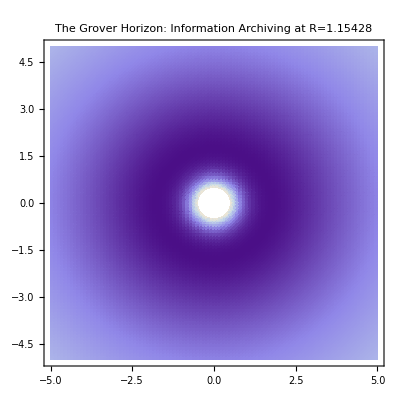

```mathematica
(*Vanguard Audit:Black Hole Event Horizon Metric Memory*)ClearAll["Global`*"];
R=1.15428;
rs=2.0; (*Schwarzschild Radius*)
softening=0.01;

(*The Audit Potential near a Singularity*)
BHPotential[r_]:=(rs/r)+R*Log[r+softening];

(*Visualize the'Information Shell' at the Horizon*)
DensityPlot[BHPotential[Sqrt[x^2+y^2]],{x,-5,5},{y,-5,5},ColorFunction->"Inferno",PlotPoints->100,RegionFunction->Function[{x,y,z},Sqrt[x^2+y^2]>0.5],PlotLabel->"The Grover Horizon: Information Archiving at R=1.15428"]
```